```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/neerajsarna/sciebo/DG_moments_deal/Mathematica_files

## Importing data

```mathematica
(*numerical solution, flag == 0,
 exact solution, flag == 1 and 
error flag == 2
error velocity space flag == 3
fe index distribution flag == 4
convergence table flag == 5*)
importdata[dof_,p_,refinetype_,flag_,outputdir_]:=Module[{result,filename},
Which[flag == 0,
filename=StringJoin["../",outputdir,"/solution/numerical_solution",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],
flag == 1,
filename=StringJoin["../",outputdir,"/solution/exact_solution",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],

flag == 2,
filename=StringJoin["../",outputdir,"/solution/error",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],
flag == 3,
filename=StringJoin["../",outputdir,"/solution/error_velocity_space",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],
flag == 4,
filename=StringJoin["../",outputdir,"/solution/fe_index",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],
flag == 5,
filename=StringJoin["../",outputdir,"/convergence_tables/convergence_table",refinetype,"degree_",ToString[p]]
];

Print[Style["Reading Data from...",FontColor->Black]];
Print[Style[ToString[filename],FontColor->Green]];
result = Import[filename,"Table"][[2;;-1,All]]
]
```

## IDs for different variables

```mathematica
(*we declare the IDs for different variables, this will help us with plotting*)
IDSpace = 1;
IDRho = 1+IDSpace;
IDvx = 2+IDSpace;
IDtheta = 3+IDSpace;
```

## Help for Plotting

```mathematica
(*we change the numerical solution obtained to the primitive variables.*)
ConvToPrim[sol_]:=Module[{factorθ,factorσ,factorq,trialsol},
trialsol = sol;
factorθ = √2;
trialsol⟦All,IDtheta⟧ =factorθ * sol⟦All,IDtheta⟧;

trialsol
]
```

### Interpolation

```mathematica
InterpolateSolution[solution_]:=Module[{densityData,vxData,vyData,thetaData,sigmaxxData,sigmaxyData,sigmayyData,qxData,qyData,pressureData},


thetaData = solution⟦All,{1,IDtheta}⟧;
(*remove the duplicate entries for Interpolation function*)
thetaData = DeleteDuplicatesBy[thetaData,First];
thetaData=Interpolation[thetaData,InterpolationOrder->1];

thetaData
]
```

### Count Fe Index

```mathematica
CountFeIndex[data_,dim_]:=Module[{FeIndices,result},
FeIndices = Range[0,10,1];
result =Flatten[ ConstantArray[0,{1,Length[FeIndices]}]];

If[dim==1,
Do[result⟦ii⟧=Count[data⟦All,2⟧,FeIndices⟦ii⟧],{ii,1,Length[result]}];,
dim==2,
Do[result⟦ii⟧=Count[data⟦All,3⟧,FeIndices⟦ii⟧],{ii,1,Length[result]}];
];

result
]
```

## Average Solution

```mathematica
AveragedSolution[solution_]:=Module[{result},
result = Flatten[ConstantArray[0,{1,Length[solution]}]];
Do[result⟦ii⟧=Sum[solution⟦jj⟧[x],{jj,1,ii}]/ii,{ii,1,Length[result]}];

result
]
```

## Poisson Heat conduction

### Discrete Velocity Solution (Kn = 0.1)

```mathematica
Arrayθ[gaussloc_,gaussW_]:=Table[gaussW⟦ii⟧(gaussloc⟦ii⟧^2-1),{ii,1,Length[gaussW]}];
```

```mathematica
exactfKn0p1=Import["/Users/neerajsarna/sciebo/DG_moments_deal/Results/Results_Discrete_Velocity/1D_Heat_Conduction/Kn0p1/fx199c80.dat","Table"];

IDpointsx=3;
IDpointsc=6;
IDdata=3;
pointscKn0p1=exactfKn0p1⟦1,IDpointsc⟧;
pointsxKn0p1=exactfKn0p1⟦1,IDpointsx⟧;
θKn0p1=Interpolation[Table[{exactfKn0p1⟦pointscKn0p1*(ii-1)+IDdata+1,1⟧-0.5,Arrayθ[exactfKn0p1⟦pointscKn0p1*(ii-1)+IDdata+1;;pointscKn0p1*(ii-1)+IDdata+pointscKn0p1,2⟧,exactfKn0p1⟦pointscKn0p1*(ii-1)+IDdata+1;;pointscKn0p1*(ii-1)+IDdata+pointscKn0p1,3⟧].exactfKn0p1⟦pointscKn0p1*(ii-1)+IDdata+1;;pointscKn0p1*(ii-1)+IDdata+pointscKn0p1,4⟧},{ii,1,pointsxKn0p1}],InterpolationOrder->3];

fKn0p1=Table[Interpolation[Table[{exactfKn0p1⟦pointscKn0p1*(ii-1)+IDdata+jj,2⟧,exactfKn0p1⟦pointscKn0p1*(ii-1)+IDdata+jj,4⟧},{jj,1,pointscKn0p1}],InterpolationOrder->3],{ii,1,pointsxKn0p1}];
```

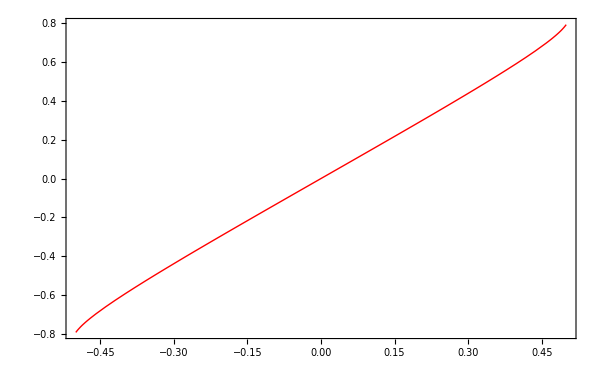

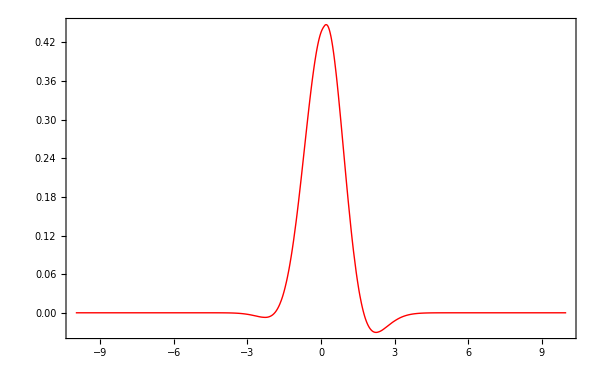

```mathematica
Plot[{θKn0p1[x]},{x,-0.5,0.5}]
Plot[{fKn0p1⟦12⟧[x]},{x,-10,10},PlotRange->Full]
```

### G20

```mathematica
ndof=3072;
foldername = "Tests/build/output_N6_poisson_heat_1D_Kn0p1";
sol=importdata[ndof,1,"_global_",0,foldername];
sol = ConvToPrim[sol];
```

#### θ

```mathematica
plot1=ListPlot[Error20⟦All,{1,IDtheta}⟧,Joined->True];
```

### G26

```mathematica
ndof=4096;
foldername = "Tests/build/output_N8_poisson_heat_1D_Kn0p1";
sol26=importdata[ndof,1,"_global_",0,foldername];
sol26 = ConvToPrim[sol26];
```

#### θ

```mathematica
plot1=ListPlot[Error20⟦All,{1,IDtheta}⟧,Joined->True];
```

### Error G20 and G26

```mathematica
ErrorG20G26 = ConstantArray[0,{Length[sol],2}];
Table[ErrorG20G26⟦ii⟧={sol⟦ii,1⟧,Abs[sol⟦ii,IDtheta⟧-sol26⟦ii,IDtheta⟧]},{ii,1,Length[sol]}];
```

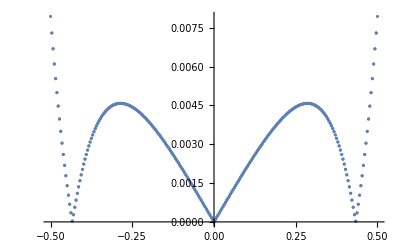

```mathematica
ListPlot[ErrorG20G26]
```

### M Adaptive

#### Pre processing

```mathematica
(*through the following routine we compute the maximum number of cells which should be present for a particular theory*)
```

```mathematica
ndofs = {20,40,80,160,320};
solutionN5Coarse = Table[importdata[ndofs⟦ii⟧,1,"_global_",0,"Tests/build/output_N5_poisson_heat_1D_Kn0p1"],{ii,1,Length[ndofs]}];
Do[solutionN5Coarse⟦ii⟧=ConvToPrim[solutionN5Coarse⟦ii⟧],{ii,1,Length[solutionN5Coarse]}];
θN5Coarse=Table[InterpolateSolution[solutionN5Coarse⟦ii⟧],{ii,1,Length[solutionN5Coarse]}];
errorθN5Coarse=Table[Sqrt[NIntegrate[(Abs[θN5Coarse⟦ii⟧[x]-θKn0p1[x]])^2,{x,-0.5,0.5}]],{ii,1,Length[θN5Coarse]}];


ndofs = {24,48,96,192,384};
solutionN6Coarse = Table[importdata[ndofs⟦ii⟧,1,"_global_",0,"Tests/build/output_N6_poisson_heat_1D_Kn0p1"],{ii,1,Length[ndofs]}];
Do[solutionN6Coarse⟦ii⟧=ConvToPrim[solutionN6Coarse⟦ii⟧],{ii,1,Length[solutionN6Coarse]}];
θN6Coarse=Table[InterpolateSolution[solutionN6Coarse⟦ii⟧],{ii,1,Length[solutionN6Coarse]}];
errorθN6Coarse=Table[Sqrt[NIntegrate[(Abs[θN6Coarse⟦ii⟧[x]-θKn0p1[x]])^2,{x,-0.5,0.5}]],{ii,1,Length[θN6Coarse]}];

ndofs = {28,56,112,224,448};
solutionN7Coarse = Table[importdata[ndofs⟦ii⟧,1,"_global_",0,"Tests/build/output_N7_poisson_heat_1D_Kn0p1"],{ii,1,Length[ndofs]}];
Do[solutionN7Coarse⟦ii⟧=ConvToPrim[solutionN7Coarse⟦ii⟧],{ii,1,Length[solutionN6Coarse]}];
θN7Coarse=Table[InterpolateSolution[solutionN7Coarse⟦ii⟧],{ii,1,Length[solutionN6Coarse]}];
errorθN7Coarse=Table[Sqrt[NIntegrate[(Abs[θN7Coarse⟦ii⟧[x]-θKn0p1[x]])^2,{x,-0.5,0.5}]],{ii,1,Length[θN6Coarse]}];

ndofs = {32,64,128,256,512};
solutionN8Coarse = Table[importdata[ndofs⟦ii⟧,1,"_global_",0,"Tests/build/output_N8_poisson_heat_1D_Kn0p1"],{ii,1,Length[ndofs]}];
Do[solutionN8Coarse⟦ii⟧=ConvToPrim[solutionN8Coarse⟦ii⟧],{ii,1,Length[solutionN8Coarse]}];
θN8Coarse=Table[InterpolateSolution[solutionN8Coarse⟦ii⟧],{ii,1,Length[solutionN8Coarse]}];
errorθN8Coarse=Table[Sqrt[NIntegrate[(Abs[θN8Coarse⟦ii⟧[x]-θKn0p1[x]])^2,{x,-0.5,0.5}]],{ii,1,Length[θN8Coarse]}];


ndofs = {48,96,192,384,768};
solutionN12Coarse = Table[importdata[ndofs⟦ii⟧,1,"_global_",0,"Tests/build/output_N12_poisson_heat_1D_Kn0p1"],{ii,1,Length[ndofs]}];
Do[solutionN12Coarse⟦ii⟧=ConvToPrim[solutionN12Coarse⟦ii⟧],{ii,1,Length[solutionN12Coarse]}];
θN12Coarse=Table[InterpolateSolution[solutionN12Coarse⟦ii⟧],{ii,1,Length[solutionN12Coarse]}];
errorθN12Coarse=Table[Sqrt[NIntegrate[(Abs[θN12Coarse⟦ii⟧[x]-θKn0p1[x]])^2,{x,-0.5,0.5}]],{ii,1,Length[θN12Coarse]}];

ndofs = {56,112,224,448,896};
solutionN14Coarse = Table[importdata[ndofs⟦ii⟧,1,"_global_",0,"Tests/build/output_N14_poisson_heat_1D_Kn0p1"],{ii,1,Length[ndofs]}];
Do[solutionN14Coarse⟦ii⟧=ConvToPrim[solutionN14Coarse⟦ii⟧],{ii,1,Length[solutionN14Coarse]}];
θN14Coarse=Table[InterpolateSolution[solutionN14Coarse⟦ii⟧],{ii,1,Length[solutionN14Coarse]}];
errorθN14Coarse=Table[Sqrt[NIntegrate[(Abs[θN14Coarse⟦ii⟧[x]-θKn0p1[x]])^2,{x,-0.5,0.5}]],{ii,1,Length[θN14Coarse]}];
```

Reading Data from...

../Tests/build/output_N5_poisson_heat_1D_Kn0p1/solution/numerical_solution_global_degree_1_DOF_20

Reading Data from...

../Tests/build/output_N5_poisson_heat_1D_Kn0p1/solution/numerical_solution_global_degree_1_DOF_40

Reading Data from...

../Tests/build/output_N5_poisson_heat_1D_Kn0p1/solution/numerical_solution_global_degree_1_DOF_80

Reading Data from...

../Tests/build/output_N5_poisson_heat_1D_Kn0p1/solution/numerical_solution_global_degree_1_DOF_160

Reading Data from...

../Tests/build/output_N5_poisson_heat_1D_Kn0p1/solution/numerical_solution_global_degree_1_DOF_320

Reading Data from...

../Tests/build/output_N6_poisson_heat_1D_Kn0p1/solution/numerical_solution_global_degree_1_DOF_24

Reading Data from...

../Tests/build/output_N6_poisson_heat_1D_Kn0p1/solution/numerical_solution_global_degree_1_DOF_48

Reading Data from...

../Tests/build/output_N6_poisson_heat_1D_Kn0p1/solution/numerical_solution_global_degree_1_DOF_96

Reading Data from...

../Tests/build/output_N6_poisson_heat_1D_Kn0p1/solution/numerical_solution_global_degree_1_DOF_192

Reading Data from...

../Tests/build/output_N6_poisson_heat_1D_Kn0p1/solution/numerical_solution_global_degree_1_DOF_384

Reading Data from...

../Tests/build/output_N7_poisson_heat_1D_Kn0p1/solution/numerical_solution_global_degree_1_DOF_28

Reading Data from...

../Tests/build/output_N7_poisson_heat_1D_Kn0p1/solution/numerical_solution_global_degree_1_DOF_56

Reading Data from...

../Tests/build/output_N7_poisson_heat_1D_Kn0p1/solution/numerical_solution_global_degree_1_DOF_112

Reading Data from...

../Tests/build/output_N7_poisson_heat_1D_Kn0p1/solution/numerical_solution_global_degree_1_DOF_224

Reading Data from...

../Tests/build/output_N7_poisson_heat_1D_Kn0p1/solution/numerical_solution_global_degree_1_DOF_448

Reading Data from...

../Tests/build/output_N8_poisson_heat_1D_Kn0p1/solution/numerical_solution_global_degree_1_DOF_32

Reading Data from...

../Tests/build/output_N8_poisson_heat_1D_Kn0p1/solution/numerical_solution_global_degree_1_DOF_64

Reading Data from...

../Tests/build/output_N8_poisson_heat_1D_Kn0p1/solution/numerical_solution_global_degree_1_DOF_128

Reading Data from...

../Tests/build/output_N8_poisson_heat_1D_Kn0p1/solution/numerical_solution_global_degree_1_DOF_256

Reading Data from...

../Tests/build/output_N8_poisson_heat_1D_Kn0p1/solution/numerical_solution_global_degree_1_DOF_512

Reading Data from...

../Tests/build/output_N12_poisson_heat_1D_Kn0p1/solution/numerical_solution_global_degree_1_DOF_48

Reading Data from...

../Tests/build/output_N12_poisson_heat_1D_Kn0p1/solution/numerical_solution_global_degree_1_DOF_96

Reading Data from...

../Tests/build/output_N12_poisson_heat_1D_Kn0p1/solution/numerical_solution_global_degree_1_DOF_192

Reading Data from...

../Tests/build/output_N12_poisson_heat_1D_Kn0p1/solution/numerical_solution_global_degree_1_DOF_384

Reading Data from...

../Tests/build/output_N12_poisson_heat_1D_Kn0p1/solution/numerical_solution_global_degree_1_DOF_768

Reading Data from...

../Tests/build/output_N14_poisson_heat_1D_Kn0p1/solution/numerical_solution_global_degree_1_DOF_56

Reading Data from...

../Tests/build/output_N14_poisson_heat_1D_Kn0p1/solution/numerical_solution_global_degree_1_DOF_112

Reading Data from...

../Tests/build/output_N14_poisson_heat_1D_Kn0p1/solution/numerical_solution_global_degree_1_DOF_224

Reading Data from...

../Tests/build/output_N14_poisson_heat_1D_Kn0p1/solution/numerical_solution_global_degree_1_DOF_448

Reading Data from...

../Tests/build/output_N14_poisson_heat_1D_Kn0p1/solution/numerical_solution_global_degree_1_DOF_896

```mathematica
DiffErrorN6 =Flatten[ ConstantArray[0,{1,Length[errorθN12Coarse]-1}]];
DiffErrorN8 =Flatten[ ConstantArray[0,{1,Length[errorθN12Coarse]-1}]];
DiffErrorN12 =Flatten[ ConstantArray[0,{1,Length[errorθN12Coarse]-1}]];
DiffErrorN14 =Flatten[ ConstantArray[0,{1,Length[errorθN12Coarse]-1}]];

Do[DiffErrorN6⟦ii⟧=Abs[errorθN6Coarse⟦ii⟧-errorθN6Coarse⟦ii+1⟧];,{ii,1,Length[DiffErrorN6]}];
Do[DiffErrorN8⟦ii⟧=Abs[errorθN8Coarse⟦ii⟧-errorθN8Coarse⟦ii+1⟧];,{ii,1,Length[DiffErrorN8]}];
Do[DiffErrorN12⟦ii⟧=Abs[errorθN12Coarse⟦ii⟧-errorθN12Coarse⟦ii+1⟧];,{ii,1,Length[DiffErrorN12]}];
Do[DiffErrorN14⟦ii⟧=Abs[errorθN14Coarse⟦ii⟧-errorθN14Coarse⟦ii+1⟧];,{ii,1,Length[DiffErrorN14]}];
```

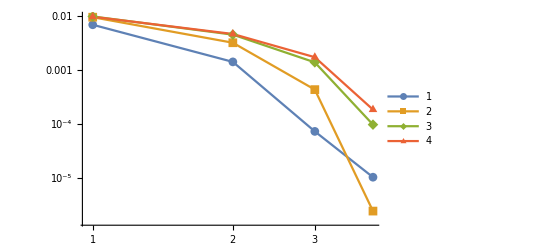

```mathematica
ListLogLogPlot[{DiffErrorN6,DiffErrorN8,DiffErrorN12,DiffErrorN14},Joined->True,PlotMarkers->Automatic,PlotLegends->Automatic]
```

```mathematica
(*now we understand the variation of the L2 norm for different moment theories*)
L2Norms = Table[{Sqrt[NIntegrate[θN5Coarse⟦ii⟧[x]^2,{x,-0.5,0.5}]],Sqrt[NIntegrate[θN6Coarse⟦ii⟧[x]^2,{x,-0.5,0.5}]],Sqrt[NIntegrate[θN7Coarse⟦ii⟧[x]^2,{x,-0.5,0.5}]],Sqrt[NIntegrate[θN8Coarse⟦ii⟧[x]^2,{x,-0.5,0.5}]],Sqrt[NIntegrate[θN12Coarse⟦ii⟧[x]^2,{x,-0.5,0.5}]],Sqrt[NIntegrate[θN14Coarse⟦ii⟧[x]^2,{x,-0.5,0.5}]]},{ii,1,Length[θN6Coarse]}];
```

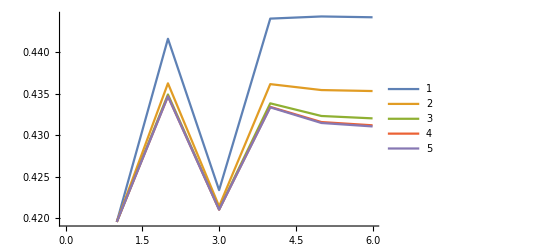

```mathematica
ListPlot[Table[L2Norms⟦ii⟧,{ii,1,Length[L2Norms]}],Joined->True,PlotLegends->Automatic]
```

#### N6

```mathematica
solutionN6 = importdata[12288,1,"_global_",0,"Results/Results_Poisson_1D_m_adaptive/output_N6_poisson_heat_1D_Kn0p1"];
solutionN6 = ConvToPrim[solutionN6];
VariationθN6 = InterpolateSolution[solutionN6];
errorθN6 = Sqrt[NIntegrate[(Abs[VariationθN6[x]-θKn0p1[x]])^2,{x,-0.5,0.5}]]
```

0.00719309

0.00623411

#### N12

```mathematica
solutionN12 = importdata[24576,1,"_global_",0,"Results/Results_Poisson_1D_m_adaptive/output_N12_poisson_heat_1D_Kn0p1"];
solutionN12 = ConvToPrim[solutionN12];
VariationθN12 = InterpolateSolution[solutionN12];
errorθN12 =Sqrt[ NIntegrate[(Abs[VariationθN12[x]-θKn0p1[x]])^2,{x,-0.5,0.5}]]
```

0.00221844

#### N6N8N12(Distribution function deviation based, FE index)

```mathematica
ndofs={12568,12664,12768,13016,13336,13744,14280,15000,16160,16496,16928,17496};

filename = Table[StringJoin["Results/Results_Poisson_1D_m_adaptive","/output_N6_N8_N12_poisson_heat_1D_Kn0p1_frac0p",ToString[ii]],{ii,6,2,-1}];
filename = Join[{"Results/Results_Poisson_1D_m_adaptive/output_N6_N8_N12_poisson_heat_1D_Kn0p1_frac0p8","Results/Results_Poisson_1D_m_adaptive/output_N6_N8_N12_poisson_heat_1D_Kn0p1_frac0p75","Results/Results_Poisson_1D_m_adaptive/output_N6_N8_N12_poisson_heat_1D_Kn0p1_frac0p7"},filename,{"Results/Results_Poisson_1D_m_adaptive/output_N6_N8_N12_poisson_heat_1D_Kn0p1_frac0p1","Results/Results_Poisson_1D_m_adaptive/output_N6_N8_N12_poisson_heat_1D_Kn0p1_frac0p08","Results/Results_Poisson_1D_m_adaptive/output_N6_N8_N12_poisson_heat_1D_Kn0p1_frac0p06",
"Results/Results_Poisson_1D_m_adaptive/output_N6_N8_N12_poisson_heat_1D_Kn0p1_frac0p04"}];
```

```mathematica
feIndexAdaptive =Table[importdata[ndofs⟦ii⟧,1,"_global_",4,filename⟦ii⟧],{ii,1,Length[filename]}];
```

Reading Data from...

../Results/Results_Poisson_1D_m_adaptive/output_N6_N8_N12_poisson_heat_1D_Kn0p1_frac0p8/solution/fe_index_global_degree_1_DOF_12568

Reading Data from...

../Results/Results_Poisson_1D_m_adaptive/output_N6_N8_N12_poisson_heat_1D_Kn0p1_frac0p75/solution/fe_index_global_degree_1_DOF_12664

Reading Data from...

../Results/Results_Poisson_1D_m_adaptive/output_N6_N8_N12_poisson_heat_1D_Kn0p1_frac0p7/solution/fe_index_global_degree_1_DOF_12768

Reading Data from...

../Results/Results_Poisson_1D_m_adaptive/output_N6_N8_N12_poisson_heat_1D_Kn0p1_frac0p6/solution/fe_index_global_degree_1_DOF_13016

Reading Data from...

../Results/Results_Poisson_1D_m_adaptive/output_N6_N8_N12_poisson_heat_1D_Kn0p1_frac0p5/solution/fe_index_global_degree_1_DOF_13336

Reading Data from...

../Results/Results_Poisson_1D_m_adaptive/output_N6_N8_N12_poisson_heat_1D_Kn0p1_frac0p4/solution/fe_index_global_degree_1_DOF_13744

Reading Data from...

../Results/Results_Poisson_1D_m_adaptive/output_N6_N8_N12_poisson_heat_1D_Kn0p1_frac0p3/solution/fe_index_global_degree_1_DOF_14280

Reading Data from...

../Results/Results_Poisson_1D_m_adaptive/output_N6_N8_N12_poisson_heat_1D_Kn0p1_frac0p2/solution/fe_index_global_degree_1_DOF_15000

Reading Data from...

../Results/Results_Poisson_1D_m_adaptive/output_N6_N8_N12_poisson_heat_1D_Kn0p1_frac0p1/solution/fe_index_global_degree_1_DOF_16160

Reading Data from...

../Results/Results_Poisson_1D_m_adaptive/output_N6_N8_N12_poisson_heat_1D_Kn0p1_frac0p08/solution/fe_index_global_degree_1_DOF_16496

Reading Data from...

../Results/Results_Poisson_1D_m_adaptive/output_N6_N8_N12_poisson_heat_1D_Kn0p1_frac0p06/solution/fe_index_global_degree_1_DOF_16928

Reading Data from...

../Results/Results_Poisson_1D_m_adaptive/output_N6_N8_N12_poisson_heat_1D_Kn0p1_frac0p04/solution/fe_index_global_degree_1_DOF_17496

```mathematica
Do[feIndexAdaptive⟦ii⟧=CountFeIndex[feIndexAdaptive⟦ii⟧,1],{ii,1,Length[feIndexAdaptive]}];
```

```mathematica
(*As per the pre processing we compute the minimum number of cells which should be present for every moment theory and then depending upon that we compute the IDs of the solution which obey this.*)
allowedIDs = {6,7,8,9,10,11,12};
feIndexAdaptive
```

{{974,40,10,0,0,0,0,0,0,0,0},{958,52,14,0,0,0,0,0,0,0,0},{944,60,20,0,0,0,0,0,0,0,0},{910,80,34,0,0,0,0,0,0,0,0},{870,100,54,0,0,0,0,0,0,0,0},{820,124,80,0,0,0,0,0,0,0,0},{758,150,116,0,0,0,0,0,0,0,0},{674,186,164,0,0,0,0,0,0,0,0},{536,248,240,0,0,0,0,0,0,0,0},{496,266,262,0,0,0,0,0,0,0,0},{444,290,290,0,0,0,0,0,0,0,0},{378,318,328,0,0,0,0,0,0,0,0}}

#### N6N8N12(Distribution function deviation based)

```mathematica
ndofs={12568,12664,12768,13016,13336,13744,14280,15000,16160,16496,16928,17496};

filename = Table[StringJoin["Results/Results_Poisson_1D_m_adaptive","/output_N6_N8_N12_poisson_heat_1D_Kn0p1_frac0p",ToString[ii]],{ii,6,2,-1}];
filename = Join[{"Results/Results_Poisson_1D_m_adaptive/output_N6_N8_N12_poisson_heat_1D_Kn0p1_frac0p8","Results/Results_Poisson_1D_m_adaptive/output_N6_N8_N12_poisson_heat_1D_Kn0p1_frac0p75","Results/Results_Poisson_1D_m_adaptive/output_N6_N8_N12_poisson_heat_1D_Kn0p1_frac0p7"},filename,{"Results/Results_Poisson_1D_m_adaptive/output_N6_N8_N12_poisson_heat_1D_Kn0p1_frac0p1","Results/Results_Poisson_1D_m_adaptive/output_N6_N8_N12_poisson_heat_1D_Kn0p1_frac0p08","Results/Results_Poisson_1D_m_adaptive/output_N6_N8_N12_poisson_heat_1D_Kn0p1_frac0p06",
"Results/Results_Poisson_1D_m_adaptive/output_N6_N8_N12_poisson_heat_1D_Kn0p1_frac0p04"}];
solutionAdaptive =Table[importdata[ndofs⟦ii⟧,1,"_global_",0,filename⟦ii⟧],{ii,1,Length[filename]}];
```

Reading Data from...

../Results/Results_Poisson_1D_m_adaptive/output_N6_N8_N12_poisson_heat_1D_Kn0p1_frac0p8/solution/numerical_solution_global_degree_1_DOF_12568

Reading Data from...

../Results/Results_Poisson_1D_m_adaptive/output_N6_N8_N12_poisson_heat_1D_Kn0p1_frac0p75/solution/numerical_solution_global_degree_1_DOF_12664

Reading Data from...

../Results/Results_Poisson_1D_m_adaptive/output_N6_N8_N12_poisson_heat_1D_Kn0p1_frac0p7/solution/numerical_solution_global_degree_1_DOF_12768

Reading Data from...

../Results/Results_Poisson_1D_m_adaptive/output_N6_N8_N12_poisson_heat_1D_Kn0p1_frac0p6/solution/numerical_solution_global_degree_1_DOF_13016

Reading Data from...

../Results/Results_Poisson_1D_m_adaptive/output_N6_N8_N12_poisson_heat_1D_Kn0p1_frac0p5/solution/numerical_solution_global_degree_1_DOF_13336

Reading Data from...

../Results/Results_Poisson_1D_m_adaptive/output_N6_N8_N12_poisson_heat_1D_Kn0p1_frac0p4/solution/numerical_solution_global_degree_1_DOF_13744

Reading Data from...

../Results/Results_Poisson_1D_m_adaptive/output_N6_N8_N12_poisson_heat_1D_Kn0p1_frac0p3/solution/numerical_solution_global_degree_1_DOF_14280

Reading Data from...

../Results/Results_Poisson_1D_m_adaptive/output_N6_N8_N12_poisson_heat_1D_Kn0p1_frac0p2/solution/numerical_solution_global_degree_1_DOF_15000

Reading Data from...

../Results/Results_Poisson_1D_m_adaptive/output_N6_N8_N12_poisson_heat_1D_Kn0p1_frac0p1/solution/numerical_solution_global_degree_1_DOF_16160

Reading Data from...

../Results/Results_Poisson_1D_m_adaptive/output_N6_N8_N12_poisson_heat_1D_Kn0p1_frac0p08/solution/numerical_solution_global_degree_1_DOF_16496

Reading Data from...

../Results/Results_Poisson_1D_m_adaptive/output_N6_N8_N12_poisson_heat_1D_Kn0p1_frac0p06/solution/numerical_solution_global_degree_1_DOF_16928

Reading Data from...

../Results/Results_Poisson_1D_m_adaptive/output_N6_N8_N12_poisson_heat_1D_Kn0p1_frac0p04/solution/numerical_solution_global_degree_1_DOF_17496

```mathematica
Do[solutionAdaptive⟦ii⟧ = ConvToPrim[solutionAdaptive⟦ii⟧],{ii,1,Length[solutionAdaptive]}];
Variationθ = Table[InterpolateSolution[solutionAdaptive⟦ii⟧],{ii,1,Length[solutionAdaptive]}];
errorθ=Table[Sqrt[NIntegrate[(Abs[Variationθ⟦ii⟧[x]-θKn0p1[x]])^2,{x,-0.5,0.5}]],{ii,1,Length[Variationθ]}];
```

```mathematica
errorθ
```

{0.00308579,0.00352999,0.00369929,0.00345327,0.00333419,0.0031729,0.00296642}

```mathematica
(*we only take those solutions which are allowed*)
plotDataAdaptive = Join[{{12288,errorθN6}},Table[{ndofs⟦ii⟧,errorθ⟦ii⟧},{ii,allowedIDs}],{{24567,errorθN12}}];
plotDataUniform = {{12288,errorθN6},{24567,errorθN12}};
```

```mathematica
plotData
```

{{12288,0.00719309},{13016,0.00224234},{13336,0.00255762},{13744,0.00308579},{14280,0.00352999},{15000,0.00369929}}

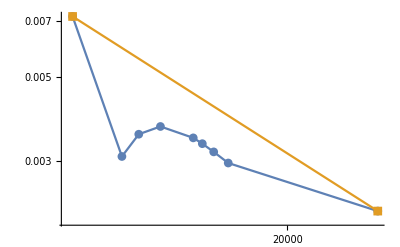

```mathematica
ListLogLogPlot[{plotDataAdaptive,plotDataUniform},PlotRange->Full,Joined->True,PlotMarkers->Automatic]
```

## Inflow

### Reference (N22)

```mathematica
ndof=11264;
foldername = "Results/Results_Inflow_1D/output_N22_inflow_1D_Kn0p1";
sol=importdata[ndof,1,"_global_",0,foldername];
sol = ConvToPrim[sol];
θRef = InterpolateSolution[sol];
```

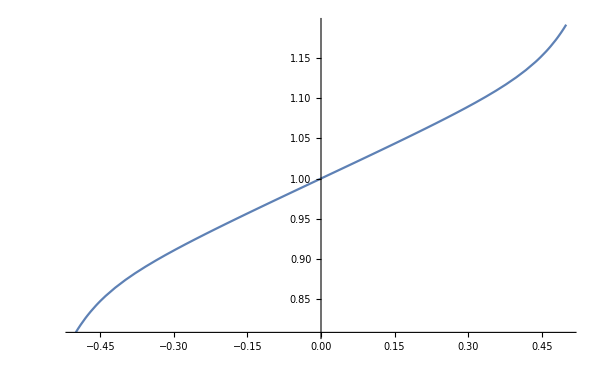

```mathematica
Plot[θRef[x],{x,-0.5,0.5}]
```

### Solutions

```mathematica
ndof={2560,3072,3584,4096,4608,5120,5632,6144,6656,7168,7680,8192};
foldername = Table[StringJoin["Results/Results_Inflow_1D/output_N",ToString[ii],"_inflow_1D_Kn0p1"],{ii,Range[5,16]}];
sol=Table[importdata[ndof⟦ii⟧,1,"_global_",0,foldername⟦ii⟧],{ii,1,Length[foldername]}];
Do[sol⟦ii⟧ = ConvToPrim[sol⟦ii⟧],{ii,1,Length[sol]}];
Variationθ = Table[InterpolateSolution[sol⟦ii⟧],{ii,1,Length[sol]}];
Averagedθ=AveragedSolution[Variationθ];
errorθ = Table[NIntegrate[Abs[Variationθ⟦ii⟧[x]-θRef[x]],{x,-0.5,0.5}],{ii,1,Length[Variationθ]}];
errorθAvg =Table[NIntegrate[Abs[Averagedθ⟦ii⟧-θRef[x]],{x,-0.5,0.5}],{ii,1,Length[Variationθ]}];
```

#### Error variation

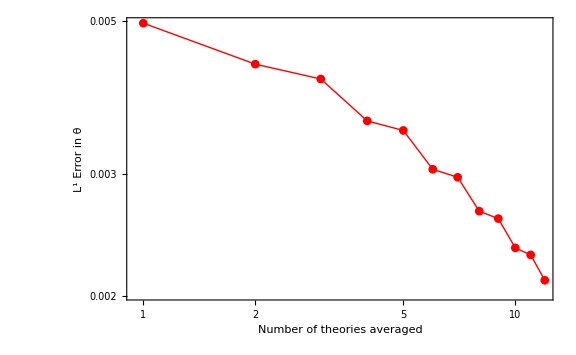

```mathematica
plot1=ListLogLogPlot[errorθAvg,Joined->True,PlotMarkers->Automatic,PlotRange->Full,GridLines->Automatic,Frame->True,PlotStyle->{Thick,Red},FrameTicksStyle->18,FrameLabel->{{Style["L^1 Error in θ",FontSize->16],None},{Style["Number of theories averaged",FontSize->16],None}},ImageSize->Large]
```

#### Field variation

```mathematica
plotThetaZoomed=Plot[{θRef[x],Variationθ⟦2⟧[x],Variationθ⟦8⟧[x]},{x,0.47,0.5},Frame->True,GridLines->False,ImageSize->10,PlotStyle->{{Black,Thick},{Darker[Green],Thick},{Red,Thick}},FrameTicksStyle->14,RotateLabel->False];

plotTheta=Plot[{θRef[x],Variationθ⟦2⟧[x],Variationθ⟦8⟧[x]},{x,0.0,0.5},Frame->True,GridLines->Automatic,ImageSize->800,PlotStyle->{{Black,Thick},{Darker[Green],Thick},{Red,Thick}},FrameTicksStyle->18,FrameLabel->{{Style["θ(x)",FontSize->16],None},{Style["x",FontSize->16],None}},RotateLabel->False,PlotLegends->Placed[{"Reference","M=5","M=11"},{0.7,0.15}],Epilog->Inset[plotThetaZoomed,{0.14,1.141},Automatic,0.3]]
```

```mathematica
?LegendPosition
```

Information::notfound: Symbol LegendPosition not found.

#### Energy Growth

```mathematica
energyGrowthN5 = Import["../Results/Results_Inflow_1D/energy_growth","Table"]⟦1;;-2⟧;
UpperBoundN5 = ConstantArray[0,{Length[energyGrowthN5],2}];
Do[UpperBoundN5⟦ii,1⟧=energyGrowthN5⟦ii,1⟧;UpperBoundN5⟦ii,2⟧=2.095;,{ii,1,Length[UpperBoundN5]}];
```

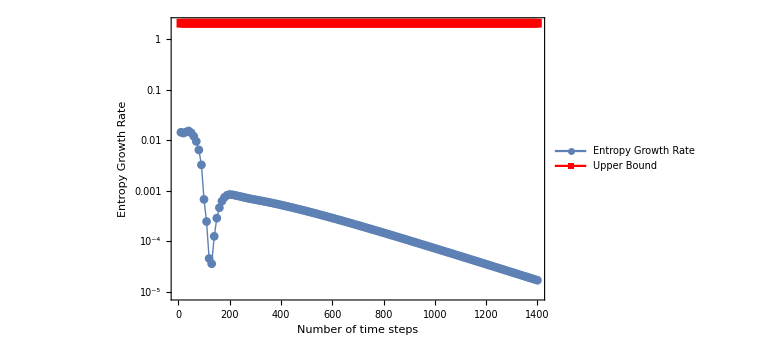

```mathematica
ListLogPlot[{Abs[energyGrowthN5],UpperBoundN5},PlotMarkers->Automatic,PlotRange->Full,GridLines->Automatic,Frame->True,PlotStyle->{Thick,Red},FrameTicksStyle->18,FrameLabel->{{Style["Entropy Growth Rate",FontSize->16],None},{Style["Number of time steps",FontSize->16],None}},ImageSize->Large,PlotLegends->Placed[{"Entropy Growth Rate","Upper Bound"},{0.7,0.4}],Joined->True]
```

```mathematica
energyGrowthN5
```

{{10.,0.0144134},{20.,0.0138995},{30.,0.0145927},{40.,0.0153359},{50.,0.0140943},{60.,0.0120402},{70.,0.0095238},{80.,0.00645681},{90.,0.00326147},{100.,0.000675599},{110.,-0.00024588},{120.,-0.0000455026},{130.,0.0000358369},{140.,0.000125232},{150.,0.000287093},{160.,0.000461562},{170.,0.000623623},{180.,0.000742796},{190.,0.000816033},{200.,0.000844362},{210.,0.000836945},{220.,0.000815338},{230.,0.000794532},{240.,0.000774071},{250.,0.000752808},{260.,0.000732456},{270.,0.000713593},{280.,0.0006963},{290.,0.000680445},{300.,0.000665655},{310.,0.000651457},{320.,0.000637392},{330.,0.00062326},{340.,0.000609091},{350.,0.000594918},{360.,0.000580735},{370.,0.000566559},{380.,0.000552425},{390.,0.000538364},{400.,0.000524409},{410.,0.000510591},{420.,0.000496932},{430.,0.00048345},{440.,0.000470158},{450.,0.000457067},{460.,0.000444189},{470.,0.00043153},{480.,0.000419099},{490.,0.000406903},{500.,0.000394945},{510.,0.00038323},{520.,0.000371762},{530.,0.000360543},{540.,0.000349575},{550.,0.000338861},{560.,0.000328399},{570.,0.00031819},{580.,0.000308234},{590.,0.000298528},{600.,0.000289073},{610.,0.000279864},{620.,0.000270901},{630.,0.00026218},{640.,0.000253698},{650.,0.000245451},{660.,0.000237437},{670.,0.000229651},{680.,0.000222089},{690.,0.000214748},{700.,0.000207622},{710.,0.000200709},{720.,0.000194002},{730.,0.000187498},{740.,0.000181193},{750.,0.000175081},{760.,0.000169158},{770.,0.00016342},{780.,0.000157862},{790.,0.000152479},{800.,0.000147267},{810.,0.000142222},{820.,0.000137338},{830.,0.000132612},{840.,0.000128039},{850.,0.000123616},{860.,0.000119337},{870.,0.000115198},{880.,0.000111197},{890.,0.000107327},{900.,0.000103587},{910.,0.000099971},{920.,0.0000964763},{930.,0.000093099},{940.,0.0000898354},{950.,0.0000866822},{960.,0.0000836358},{970.,0.0000806929},{980.,0.0000778502},{990.,0.0000751047},{1000.,0.0000724531},{1010.,0.0000698925},{1020.,0.00006742},{1030.,0.0000650326},{1040.,0.0000627277},{1050.,0.0000605026},{1060.,0.0000583545},{1070.,0.0000562811},{1080.,0.0000542797},{1090.,0.0000523481},{1100.,0.0000504838},{1110.,0.0000486847},{1120.,0.0000469486},{1130.,0.0000452733},{1140.,0.0000436568},{1150.,0.0000420971},{1160.,0.0000405922},{1170.,0.0000391403},{1180.,0.0000377397},{1190.,0.0000363884},{1200.,0.0000350849},{1210.,0.0000338275},{1220.,0.0000326146},{1230.,0.0000314447},{1240.,0.0000303163},{1250.,0.000029228},{1260.,0.0000281783},{1270.,0.0000271659},{1280.,0.0000261895},{1290.,0.000025248},{1300.,0.0000243399},{1310.,0.0000234643},{1320.,0.0000226198},{1330.,0.0000218056},{1340.,0.0000210204},{1350.,0.0000202633},{1360.,0.0000195332},{1370.,0.0000188293},{1380.,0.0000181506},{1390.,0.0000174962},{1400.,0.0000168652}}

## Time Stepping

```mathematica
solutionID = Range[10,400,10];
filename = Table[StringJoin["solution_",ToString[ii]],{ii,solutionID}];
TimeSteppingSolution = Table[Import[StringJoin["../Tests/build/",ii],"Table"],{ii,filename}];
Do[TimeSteppingSolution⟦ii⟧=ConvToPrim[TimeSteppingSolution⟦ii⟧],{ii,1,Length[TimeSteppingSolution]}];
```

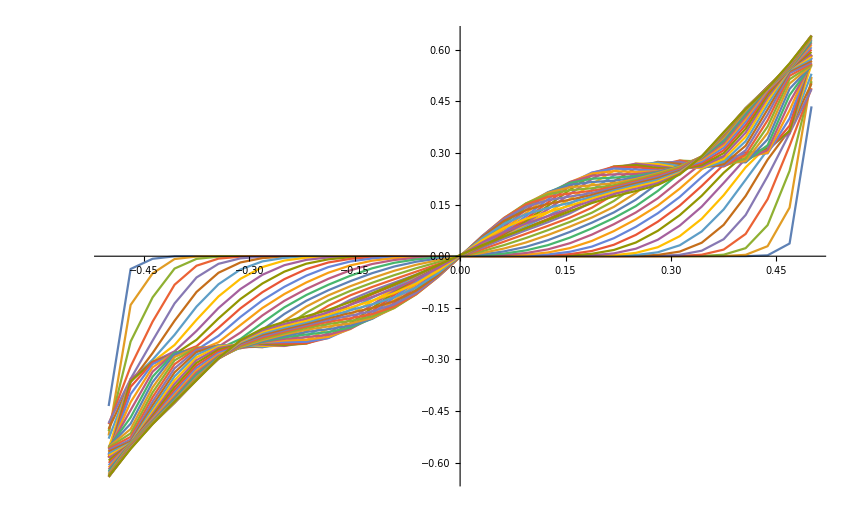

```mathematica
ListPlot[Table[TimeSteppingSolution⟦ii⟧⟦All,{1,IDtheta}⟧,{ii,1,Length[TimeSteppingSolution]}],Joined->True]
```